```mathematica
vr[r_,θ_]:=  R[r] Cos[θ];
uθ[r_,θ_]:= Θ[r] Sin[θ];
uz[r_,θ_]:=0.0;
pL[r_,θ_]:=μ P[r] Cos[θ];
```

Boundary condition are all identically satisfied if the part of conditions is independent of θ:

```mathematica
R[b] = U; Θ[b] = -U;
```

The part of the boundary conditions independent of y are then satisfied if:

```mathematica
R[a]=0;aΘ'[a] = Θ[a] + R[a];
```

Solutions are:

```mathematica
R[r_] := (2 Log[r/a] (a^4+b^4)-b^2(r^2-a^4/r^2))/(2Log[b/a](a^4+b^4)-(b^4-a^4))U;
Θ[r_]:= (2 Log[r/a] (a^4+b^4)+2(a^4+b^4)-b^2(3 r^2+a^4/r^2))/(2 Log[b/a](a^4+b^4)-(b^4-a^4))U;
P[r_]:= -4(2 r b^2 +(a^4+b^4)/r)/(2 Log[b/a](a^4+b^4)-(b^4-a^4))U;
```

Likewise a z-dependent portion to the solution of the form:

```mathematica
vr[z_,r_]:= Cos[(n π z)/h] Rn[r];
uz[z_,r_]:= Sin[n π z/h]Zn[r];
pl[z_,r_]:= Subscript[μ, E] Cos[(n π z)/h]Pn[r];
```

```mathematica
Pn[rn_]:=(2 n π)/h(A BesselK[0,rn] + B BesselI[0,rn]);
Rn[rn_]:= A rn BesselK[0,rn] + B rn BesselI[0,rn]+𝒞 BesselK[1,rn] + 𝒟 BesselI[1,rn];
Zn[rn_]:= A *(rn BesselK[1,rn]-2 BesselK[0,rn])-B*(rn BesselI[1,rn]+2 BesselI[0,rn])+𝒞 BesselK[0,rn]-𝒟*BesselI[0,rn];
```

Simple special case where the weld pool is so large that S/L boundary can be considered arbitrarily far away:

```mathematica
A=(-w0 γ h^2)/(π^2 a^2 μ)* 1/(n^2 BesselK[1,n π a/h]);
𝒞=(w0 γ h)/(π a μ)*BesselK[0,n π a/h]/(n(BesselK[1,n π a/h])^2);
B=0; 𝒟=0;
```

```mathematica
w0=1; γ=0.1; a=1; h=10; b=10;μ=0.2; n=1;
```

```mathematica
A
```

-1.74718

```mathematica
𝒟
```

0

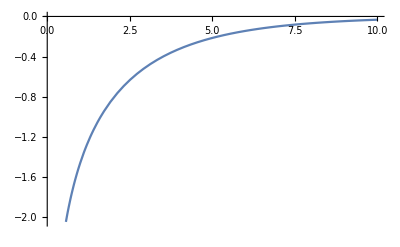

```mathematica
Plot[Pn[n π r/h],{r,0.1,10}]
```